把两副扑克牌108张随机发给4家，庄家33张牌。计算每家有特殊牌型（例如：同花顺、炸弹）的概率。

```mathematica
distributor[]:=Module[{cards=Range[13],card=0},Do[cards=Join[cards,cards],3];cards=Join[cards,{14,15,14,15}];
a={};b={};c={};d={};
Do[l=Length[cards];card=RandomInteger[{1,l}];a=AppendTo[a,cards[[card]]];cards=Delete[cards,card],25];
Do[l=Length[cards];card=RandomInteger[{1,l}];b=AppendTo[b,cards[[card]]];cards=Delete[cards,card],25];
Do[l=Length[cards];card=RandomInteger[{1,l}];c=AppendTo[c,cards[[card]]];cards=Delete[cards,card],25];
d=cards;{a,b,c,d}]
```

## Not considering the joker:

先考虑庄家拥有炸弹数目的分布：

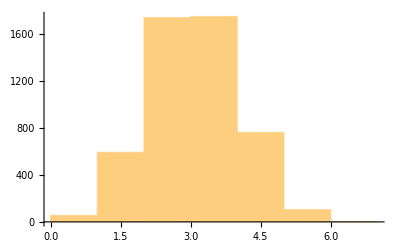

```mathematica
tab=Table[distributor[];Count[Tally[d],{_,n_/;n≥4}],{5000}];Histogram[tab]
```

似乎近似是正态分布，所以求了一下均值和方差进行拟合，发现效果很好

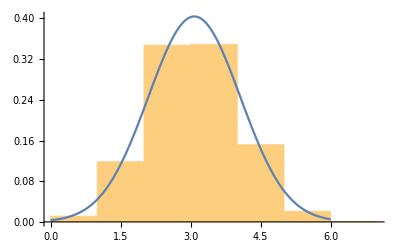

```mathematica
μ=Mean[tab];
σ=Variance[tab];Show[Histogram[tab,Automatic,"ProbabilityDensity"],Plot[PDF[NormalDistribution[μ+0.5,σ],x],{x,Min[tab],Max[tab]},PlotRange->All]]
```

再任取一个非庄家对其分布进行计算，发现并不能很好的拟合正态分布，而且其分布呈不对称性态，与正态分布有个比较大的偏移，先尝试了Poisson分布但是也无法拟合

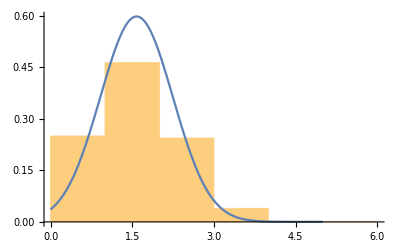

```mathematica
tab=Table[distributor[];Count[Tally[a],{_,n_/;n≥4}],{5000}];
μ=Mean[tab];
σ=Variance[tab];Show[Histogram[tab,Automatic,"ProbabilityDensity"],Plot[PDF[NormalDistribution[μ+0.5,σ],x],{x,Min[tab],Max[tab]},PlotRange->All]]
```

重新思考后发现，如果补上对称的-1，-2部分图像，重新计算均值和方差，会发现确实也拟合的很好

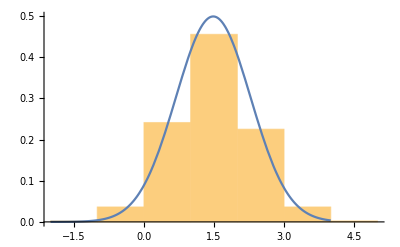

```mathematica
tab=Table[distributor[];Count[Tally[b],{_,n_/;n≥4}],{5000}];
tab=Join[tab,Table[-1,{Count[tab,n_/;n==3]}]];

tab=Join[tab,Table[-2,{Count[tab,n_/;n==4]}]];
μ=Mean[tab];
σ=Variance[tab];Show[Histogram[tab,Automatic,"ProbabilityDensity"],Plot[PDF[NormalDistribution[μ+0.5,σ],x],{x,Min[tab],Max[tab]},PlotRange->All]]
```

于是我们大胆预测这一类炸弹牌型分布满足正态分布

接下来我们讨论一下这一分牌模式的合理性，我们知道一般一次牌中的炸弹个数就很大程度上决定了一局的输赢，我们就来比较一下庄家和其他人的炸弹个数

3.2108

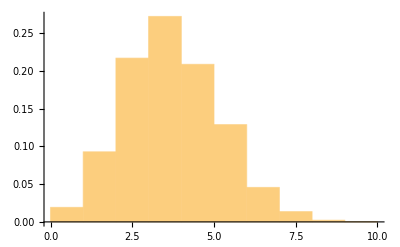

```mathematica
tab=Table[distributor[];Count[Tally[a],{_,n_/;n≥4}]+Count[Tally[b],{_,n_/;n≥4}]+Count[Tally[c],{_,n_/;n≥4}],{5000}];
μ=N[Mean[tab]]

σ=Variance[tab];Show[Histogram[tab,Automatic,"ProbabilityDensity"]]
```

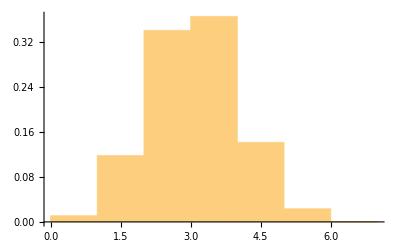

2.5792

```mathematica
tab=Table[distributor[];Count[Tally[d],{_,n_/;n≥4}],{5000}];Show[Histogram[tab,Automatic,"ProbabilityDensity"]]
μ=N[Mean[tab]]
```

## Considering the joker：

如果考虑大小王都可以替代作为炸弹牌型的一部分，那么情况会变得略微复杂一点，但是实际上也只需要外加考虑3个同样的带一个大小王的情况(这里我们考虑让炸弹尽可能得多，但是不拆8个的变成2个4个的)先考虑庄家的情况

```mathematica
distributor[];Count[Tally[d],{_,n_/;n≥4}]+Min[{Count[d,14]+Count[d,15],Count[Tally[d],{_,n_/;n==3}]}]
Tally[d]
```

5

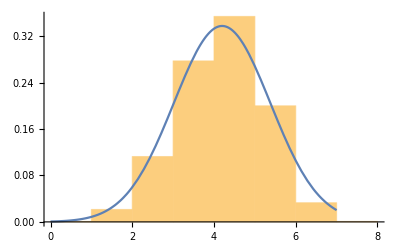

```mathematica
tab=Table[distributor[];Count[Tally[d],{_,n_/;n≥4}]+Min[{Count[d,14]+Count[d,15],Count[Tally[d],{_,n_/;n==3}]}],{5000}];
μ=Mean[tab];
σ=Variance[tab];Show[Histogram[tab,Automatic,"ProbabilityDensity"],Plot[PDF[NormalDistribution[μ+0.5,σ],x],{x,Min[tab],Max[tab]},PlotRange->All]]
```

明显的这已经不能用简单的正态分布拟合了，而更像是多个正态分布以及其他分布的叠加，只能简单地看看方差的大致情况。 

然后再是其他人的情况

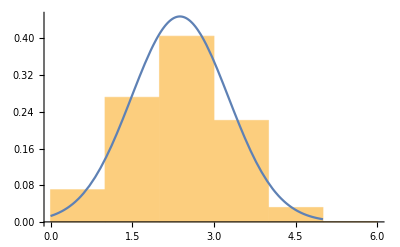

```mathematica
tab=Table[distributor[];Count[Tally[a],{_,n_/;n≥4}]+Min[{Count[a,14]+Count[a,15],Count[Tally[a],{_,n_/;n==3}]}],{5000}];
μ=Mean[tab];
σ=Variance[tab];Show[Histogram[tab,Automatic,"ProbabilityDensity"],Plot[PDF[NormalDistribution[μ+0.5,σ],x],{x,Min[tab],Max[tab]},PlotRange->All]]
```

可以看出这里的分布明显还是像同一类分布。